```mathematica
(*This is the path that contains the executables and loads SDPB*)
executablesPath = "/home/pano/.local/src/sdpb/build";
<<"/home/pano/.local/src/sdpb/mathematica/SDPB.m";
```

# Gap Consistency Checks

## We constrain possible values for the Gap of a CFT by searching for a functional which breaks everything hehe.

## Defining the Matrix Problem

Let’s first construct the matrix problem and tell SDPB to export the description into a JSON file for SDPB to actually run the thing.

{-9.42478,-580.115,-15067.7,216883.,-908427.,-1.58481×10^8,1.59243×10^10,-1.35479×10^12,1.11714×10^14,-7.67389×10^15,-3.82185×10^16,2.13846×10^20,-7.52241×10^22,2.04907×10^25 }

terminateReason = "found primal-dual optimal solution";
primalObjective = -0.05051719323674061610735081359870284473442902559596171326610311682411654426440138;
dualObjective   = -0.05051719323674061611085697045056632109291234655909873532722019273882300553803509;
dualityGap      = 3.506156851863476358483320963137022061117075914706461273633702800539227429186089e-21;
primalError     = 9.400835646101326765842328981871546478518552699188409378313885504013674673644694e-39;
dualError       = 4.261629227905433354684678689414240498745449124882923229779695762288060134444987e-45;
Solver runtime  = 2;

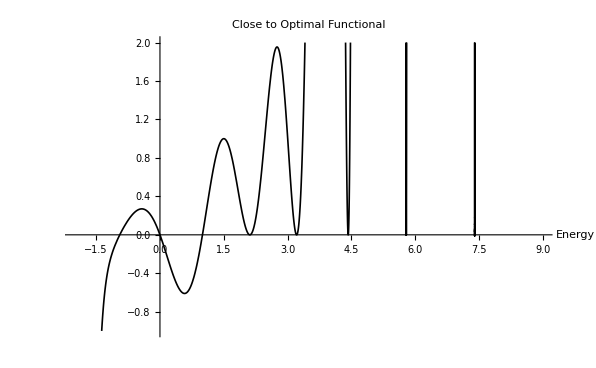

```mathematica
(*Precision and directories*)
precision = 1024;
file ="/home/pano/projects/sdpb-test/pmp.json";
sdpdir="/home/pano/projects/sdpb-test/sdp";
outdir="/home/pano/projects/sdpb-test/out";
outfile ="/home/pano/projects/sdpb-test/out/z.txt";
Run[StringRiffle[{
"rm -rf",
FileNameJoin[sdpdir,"*"],
sdpdir<>".ck",
FileNameJoin[outdir,"*"]
}]];

(*Maximum order of derivatives in the linear functional a*)
P=27; 

(*Central charge*)
c = 12; 

(*Gap energy*)
E0=1; 

(*Polynomial generator function*)
poly[n_,E0_,x_]:=Sum[StirlingS2[n,k](-2π (x+E0))^k,{k,1,n}]; 

(*Construct a module that does this whole sdpb definition thingy*)
solve[gapEnergy_:E0,centralCharge_:c, order_:P, precision_:prec]:=
Module[{
E0=gapEnergy,
c=centralCharge,
NN=Floor[order/2],
prec=precision,
objective,
normalization,
matrices
},

(*Objective vector*)
(*objective = {0}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN]);*)
objective = (poly[2#+1,0,-c/12]&/@Range[0,NN]);

(*Normalization vector*)
(*normalization = (Range[0,NN]*0);*)
normalization = (poly[2#+1,E0,0.5]&/@Range[0,NN]);
Echo[normalization];

(*Polynomial list*)
matrices={
PositiveMatrixWithPrefactor[<|
(*"polynomials"->{{{-x}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
"polynomials"->{{(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}
|>]
};

(*Define SDP*)
WritePmpJson[file, SDP[objective,normalization,matrices], prec];

(*Run the magical code to solve*)
Run[StringRiffle[{
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[prec], file, sdpdir
}]];
Run[StringRiffle[{
"mpirun",
FileNameJoin[{executablesPath,"sdpb"}],
"-s", sdpdir, "-o", outdir,
"--precision", ToString[prec],
"--noFinalCheckpoint"
,"--maxIterations",ToString[1000]
,"--dualityGapThreshold 1e-20"
, "--writeSolution=\"x,y,z\""
}]];
(*ToExpression@Import[FileNameJoin[{outdir,"out.txt"}],"Text"];*)
fullResult = Import[FileNameJoin[{outdir,"out.txt"}], "String"]
];
solve[]
(* Get the optimal vector *)
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Plot[α,{x,-c/12-E0,9},PlotRange->{-1,2} ,MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

```mathematica
(*StringRiffle[{
"rm -rf",
FileNameJoin[sdpdir,"*"],
sdpdir<>".ck",
FileNameJoin[outdir,"*"],
"&&",
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[prec], file, sdpdir,
 "&&",
"mpirun",
FileNameJoin[{executablesPath,"sdpb"}],
"-s", sdpdir, "-o", outdir,
"--precision", ToString[prec],
"--noFinalCheckpoint"
,"--maxIterations",ToString[1000]
,"--dualityGapThreshold 1e-10"
, "--writeSolution=\"x,y,z\""
}]*)
```